# Finding a see - saw structure for the matrices

## Construction of the potential

```mathematica
Quit[]
```

```mathematica
n=2
```

2

```mathematica
Clear[n]
```

#### Defining our parameters and putting the symmetries

```mathematica
(*Hermitian*)
SetAttributes[μ,Orderless]
(*Hermitian*)
For[a=1,a<=n,a++,For[b=1,b<=n,b++,For[c=1,c<=n,c++,For[d=1,d<=n,d++,λ[b,a,d,c]=λ[c,d,a,b] =λ[a,b,c,d] ]]]]
(*Z2 symmetry (softly brocken), comment or uncomment if you want to apply it*)
For[a=1,a<=n,a++,For[b=1,b<=n,b++,For[c=1,c<=n,c++,For[d=1,d<=n,d++,If [(a!=b && a!=c && a!=d),λ[a,b,c,d]=λ[b,a,c,d]=λ[c,b,a,d]=λ[d,b,c,a]=0 ]]]]]
```

```mathematica
Clear[μ,λ,β,v,h]
```

```mathematica
Array[μ,{n,n}]//MatrixForm
Array[λ,{n,n,n,n}]//MatrixForm
```

(μ[1,1] | μ[1,2]
μ[1,2] | μ[2,2])

((λ[1,1,1,1] | 0
0 | λ[1,1,2,2]) | (0 | λ[1,2,1,2]
λ[1,2,2,1] | 0)
(0 | λ[1,2,2,1]
λ[1,2,1,2] | 0) | (λ[1,1,2,2] | 0
0 | λ[2,2,2,2]))

```mathematica
V=-Sum[μ[i,j]Phidag[i].Phi[j],{i,1,n},{j,1,n}]+Sum[λ[i,j,k,l](Phidag[i].Phi[j])(Phidag[k].Phi[l]),{i,1,n},{j,1,n},{k,1,n},{l,1,n}]
```

1/4 (h[1]+v[1])^4 λ[1,1,1,1]+1/2 (h[1]+v[1])^2 (h[2]+v[2])^2 λ[1,1,2,2]+1/2 (h[1]+v[1])^2 (h[2]+v[2])^2 λ[1,2,1,2]+1/2 (h[1]+v[1])^2 (h[2]+v[2])^2 λ[1,2,2,1]+1/4 (h[2]+v[2])^4 λ[2,2,2,2]-1/2 (h[1]+v[1])^2 μ[1,1]-(h[1]+v[1]) (h[2]+v[2]) μ[1,2]-1/2 (h[2]+v[2])^2 μ[2,2]

#### Expanding around the vacuum and looking for the minimum of the potential

```mathematica
Clear[Phi,Phidag]
```

```mathematica
(*doublets with only the minimums:*)
Phi[i_]:=1/Sqrt[2]{0,v[i]}
Phidag[i_]:=1/Sqrt[2]{0,v[i]}
```

#### Fields in the normal basis

```mathematica
(*Fields without the minimum*)
Phi[i_]=1/Sqrt[2]{0,v[i]+h[i]};
Phidag[i_]=1/Sqrt[2]{0,v[i]+h[i]};
```

#### Fields in the higgs basis

```mathematica
(*Fields without the minimum*)
Phi[i_]=1/Sqrt[2]{0,h[i]};
Phidag[i_]=1/Sqrt[2]{0,h[i]};
```

```mathematica
(*Field 1 with the minimum:*)
Phi[1]=1/Sqrt[2]{0,v+h[1]};
Phidag[1]=1/Sqrt[2]{0,v+h[1]};
```

#### Transformation of the vevs and the fields to the higgs basis:

```mathematica
Vmiddle=v;
For[i=0,i<n-1,i++,
(*Print[i];
Print[{0,Vmiddle}];*)
{v[n-i-1],v[n-i]}={{Cos[β[n-i-1]], Sin[β[n-i-1]]},{-Sin[β[n-i-1]], Cos[β[n-i-1]]}}.{0,Vmiddle};
b=Vmiddle;
Clear[Vmiddle];
Vmiddle=Sin[β[n-i-1]]b]
Hm=H[1];
For[i=0,i<n-1,i++,
(*Print[i];
Print[{0,Vmiddle}];*)
{h[1],h[n-i]}={{Cos[β[n-i-1]], Sin[β[n-i-1]]},{-Sin[β[n-i-1]], Cos[β[n-i-1]]}}.{Hm,H[n-i]};
(*Print[{ρ[1],ρ[n-1]}];*)
b=h[1];
Clear[Hm];
Hm=b;]
```

#### Rotation angle:

```mathematica
Clear[a,b,c,d]
```

```mathematica
MassMatrix={{a,c1},{c1,b}}
(*MassMatrix={{a,c1,c2},{c1,b,o},{c2,o,c}}*)
(*MassMatrix={{a,c1,c2,c3},{c1,b,o,o},{c2,o,c,o},{c3,0,0,d}}*)
```

{{a,c1},{c1,b}}

```mathematica
(* In this for we do each rotation, i.e. we calculate the angle relative to every rotation and how will change the first entry of the matrix after each rotation*)
For[i=1,i<n,i++,
θ[i]=N[1/2 ArcTan[2MassMatrix[[1,i+1]]/(-MassMatrix[[1,1]]+MassMatrix[[i+1,i+1]])]];
MassMatrix[[1,1]]=Cos[θ[i]]^2 MassMatrix[[1,1]]-2 Cos[θ[i]] MassMatrix[[1,i+1]]^2 Sin[θ[i]]+MassMatrix[[i+1,i+1]]^2 Sin[θ[i]]^2;]
```

```mathematica
θ[1]
θ[2]
θ[3]
```

0.5 ArcTan[(2. c1)/(-1. a+b)]

0.5 ArcTan[(2. c2)/(c-1. a Cos[0.5 ArcTan[(2. c1)/(-1. a+b)]]^2+2. c1^2 Cos[0.5 ArcTan[(2. c1)/(-1. a+b)]] Sin[0.5 ArcTan[(2. c1)/(-1. a+b)]]-1. b^2 Sin[0.5 ArcTan[(2. c1)/(-1. a+b)]]^2)]

# 2 x2

### Expanding around the minimum

```mathematica
Simplify[Solve[{D[V,v[1]]==0,D[V,v[2]]==0}, {μ[1,1],μ[2,2]} ]]//Simplify
```

{{μ[1,1]→1/(4 v[1])(4 v[1]^3 λ[1,1,1,1]+3 v[1]^2 v[2] (λ[1,1,1,2]+λ[1,1,2,1]+λ[1,2,1,1]+λ[2,1,1,1])+2 v[1] v[2]^2 (λ[1,1,2,2]+λ[1,2,1,2]+λ[1,2,2,1]+λ[2,1,1,2]+λ[2,1,2,1]+λ[2,2,1,1])+v[2]^3 (λ[1,2,2,2]+λ[2,1,2,2]+λ[2,2,1,2]+λ[2,2,2,1])-4 v[2] μ[1,2]),μ[2,2]→1/(4 v[2])(v[1]^3 (λ[1,1,1,2]+λ[1,1,2,1]+λ[1,2,1,1]+λ[2,1,1,1])+2 v[1]^2 v[2] (λ[1,1,2,2]+λ[1,2,1,2]+λ[1,2,2,1]+λ[2,1,1,2]+λ[2,1,2,1]+λ[2,2,1,1])+4 v[2]^3 λ[2,2,2,2]+v[1] (3 v[2]^2 (λ[1,2,2,2]+λ[2,1,2,2]+λ[2,2,1,2]+λ[2,2,2,1])-4 μ[1,2]))}}

```mathematica
{μ[1,1],μ[2,2]}={1/(4 v[1])(4 v[1]^3 λ[1,1,1,1]+3 v[1]^2 v[2] (λ[1,1,1,2]+λ[1,1,2,1]+λ[1,2,1,1]+λ[2,1,1,1])+2 v[1] v[2]^2 (λ[1,1,2,2]+λ[1,2,1,2]+λ[1,2,2,1]+λ[2,1,1,2]+λ[2,1,2,1]+λ[2,2,1,1])+v[2]^3 (λ[1,2,2,2]+λ[2,1,2,2]+λ[2,2,1,2]+λ[2,2,2,1])-4 v[2] μ[1,2]),1/(4 v[2])(v[1]^3 (λ[1,1,1,2]+λ[1,1,2,1]+λ[1,2,1,1]+λ[2,1,1,1])+2 v[1]^2 v[2] (λ[1,1,2,2]+λ[1,2,1,2]+λ[1,2,2,1]+λ[2,1,1,2]+λ[2,1,2,1]+λ[2,2,1,1])+4 v[2]^3 λ[2,2,2,2]+v[1] (3 v[2]^2 (λ[1,2,2,2]+λ[2,1,2,2]+λ[2,2,1,2]+λ[2,2,2,1])-4 μ[1,2]))}
```

{1/(4 v)Csc[β[1]] (4 v^3 Sin[β[1]]^3 λ[1,1,1,1]+2 v^3 Cos[β[1]]^2 Sin[β[1]] (2 λ[1,1,2,2]+2 λ[1,2,1,2]+2 λ[1,2,2,1])-4 v Cos[β[1]] μ[1,2]),1/(4 v)Sec[β[1]] (2 v^3 Cos[β[1]] Sin[β[1]]^2 (2 λ[1,1,2,2]+2 λ[1,2,1,2]+2 λ[1,2,2,1])+4 v^3 Cos[β[1]]^3 λ[2,2,2,2]-4 v Sin[β[1]] μ[1,2])}

```mathematica
V2=V
```

1/4 (Cos[β[1]] H[1]+v Sin[β[1]]+H[2] Sin[β[1]])^4 λ[1,1,1,1]+1/2 (v Cos[β[1]]+Cos[β[1]] H[2]-H[1] Sin[β[1]])^2 (Cos[β[1]] H[1]+v Sin[β[1]]+H[2] Sin[β[1]])^2 λ[1,1,2,2]+1/2 (v Cos[β[1]]+Cos[β[1]] H[2]-H[1] Sin[β[1]])^2 (Cos[β[1]] H[1]+v Sin[β[1]]+H[2] Sin[β[1]])^2 λ[1,2,1,2]+1/2 (v Cos[β[1]]+Cos[β[1]] H[2]-H[1] Sin[β[1]])^2 (Cos[β[1]] H[1]+v Sin[β[1]]+H[2] Sin[β[1]])^2 λ[1,2,2,1]+1/4 (v Cos[β[1]]+Cos[β[1]] H[2]-H[1] Sin[β[1]])^4 λ[2,2,2,2]-(v Cos[β[1]]+Cos[β[1]] H[2]-H[1] Sin[β[1]]) (Cos[β[1]] H[1]+v Sin[β[1]]+H[2] Sin[β[1]]) μ[1,2]-1/(8 v)Csc[β[1]] (Cos[β[1]] H[1]+v Sin[β[1]]+H[2] Sin[β[1]])^2 (4 v^3 Sin[β[1]]^3 λ[1,1,1,1]+2 v^3 Cos[β[1]]^2 Sin[β[1]] (2 λ[1,1,2,2]+2 λ[1,2,1,2]+2 λ[1,2,2,1])-4 v Cos[β[1]] μ[1,2])-1/(8 v)Sec[β[1]] (v Cos[β[1]]+Cos[β[1]] H[2]-H[1] Sin[β[1]])^2 (2 v^3 Cos[β[1]] Sin[β[1]]^2 (2 λ[1,1,2,2]+2 λ[1,2,1,2]+2 λ[1,2,2,1])+4 v^3 Cos[β[1]]^3 λ[2,2,2,2]-4 v Sin[β[1]] μ[1,2])

```mathematica
(*Creates de Mass matrix squared of the potential with two higges*)
MassMatrix2=Table[D[D[V2,H[i]],H[j]],{i,n},{j,n}]/.H[i_]->0 //Simplify
```

{{Cot[β[1]] (2 v^2 Cos[β[1]] Sin[β[1]]^3 (λ[1,1,1,1]-2 λ[1,1,2,2]-2 λ[1,2,1,2]-2 λ[1,2,2,1]+λ[2,2,2,2])+Cos[β[1]]^2 μ[1,2]+Sin[β[1]]^2 (2+Tan[β[1]]^2) μ[1,2]),-1/2 v^2 Sin[2 β[1]] (-λ[1,1,1,1]+λ[2,2,2,2]+Cos[2 β[1]] (λ[1,1,1,1]-2 λ[1,1,2,2]-2 λ[1,2,1,2]-2 λ[1,2,2,1]+λ[2,2,2,2]))},{-1/2 v^2 Sin[2 β[1]] (-λ[1,1,1,1]+λ[2,2,2,2]+Cos[2 β[1]] (λ[1,1,1,1]-2 λ[1,1,2,2]-2 λ[1,2,1,2]-2 λ[1,2,2,1]+λ[2,2,2,2])),2 v^2 (Sin[β[1]]^4 λ[1,1,1,1]+1/2 Sin[2 β[1]]^2 (λ[1,1,2,2]+λ[1,2,1,2]+λ[1,2,2,1])+Cos[β[1]]^4 λ[2,2,2,2])}}

```mathematica
{{a,c1},{c1,b}}=MassMatrix2
```

{{Cot[β[1]] (2 v^2 Cos[β[1]] Sin[β[1]]^3 (λ[1,1,1,1]-2 λ[1,1,2,2]-2 λ[1,2,1,2]-2 λ[1,2,2,1]+λ[2,2,2,2])+Cos[β[1]]^2 μ[1,2]+Sin[β[1]]^2 (2+Tan[β[1]]^2) μ[1,2]),-1/2 v^2 Sin[2 β[1]] (-λ[1,1,1,1]+λ[2,2,2,2]+Cos[2 β[1]] (λ[1,1,1,1]-2 λ[1,1,2,2]-2 λ[1,2,1,2]-2 λ[1,2,2,1]+λ[2,2,2,2]))},{-1/2 v^2 Sin[2 β[1]] (-λ[1,1,1,1]+λ[2,2,2,2]+Cos[2 β[1]] (λ[1,1,1,1]-2 λ[1,1,2,2]-2 λ[1,2,1,2]-2 λ[1,2,2,1]+λ[2,2,2,2])),2 v^2 (Sin[β[1]]^4 λ[1,1,1,1]+1/2 Sin[2 β[1]]^2 (λ[1,1,2,2]+λ[1,2,1,2]+λ[1,2,2,1])+Cos[β[1]]^4 λ[2,2,2,2])}}

### Random Scan

```mathematica
mass={};
mu=500^2;
lambda=0.13;
count2=0;
countalign2=0;
For[i=1,i<=1000,i++,
For[a1=1,a1<=n,a1++,For[b1=1,b1<=n,b1++,μ[a1,b1]=RandomReal[{0.5, 1.5}]*mu ]];
For[a1=1,a1<=n,a1++,For[b1=1,b1<=n,b1++,For[cm=1,cm<=n,cm++,For[dm=1,dm<=n,dm++,λ[a1,b1,cm,dm]=RandomReal[{0.5, 1.5}]*lambda ]]]];
β[i]=RandomReal[{0, 1}];
v=RandomReal[{0.5, 1.5}]*246; 
(*Print[{a,b}];
Print[Cos[θ[1]]Cos[θ[2]]];*)
AppendTo[mass,{Cos[θ[1]],Eigenvalues[MassMatrix2][[2]]}];
If[Cos[θ[1]]>=0.96 && Eigenvalues[MassMatrix2][[2]]<15000,countalign2++];
If[Eigenvalues[MassMatrix2][[2]]<15000,count2++]]
```

```mathematica
(*Counts where the mass is lower than 125 GeV*)
count2
(*Counts where the mass is lower than 125 GeV and it is aligned*)countalign2
```

379

379

```mathematica
MinMax[mass[[All,2]]]
```

{3218.6,61345.3}

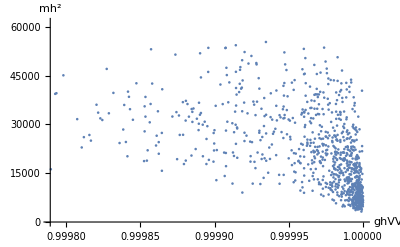

```mathematica
ListPlot[mass,AxesLabel->{ghVV,Indexed[m,h]^2}(*,PlotRange->{{0.99,1},{0,100000}}*)]
```

## 3x3

```mathematica
Simplify[Solve[{D[V,v[1]]==0,D[V,v[2]]==0,D[V,v[3]]==0}, {μ[1,1],μ[2,2],μ[3,3]} ]]//Simplify
```

{{μ[1,1]→1/v[1](v[1]^3 λ[1,1,1,1]+3 v[1]^2 (v[2] λ[1,1,1,2]+v[3] λ[1,1,1,3])+v[2]^3 λ[1,2,2,2]+v[2]^2 v[3] (λ[1,2,2,3]+λ[1,2,3,2]+λ[1,3,2,2])+v[1] (v[2]^2 (λ[1,1,2,2]+λ[1,2,1,2]+λ[1,2,2,1])+2 v[2] v[3] (λ[1,1,2,3]+λ[1,2,1,3]+λ[1,3,2,1])+v[3]^2 (λ[1,1,3,3]+λ[1,3,1,3]+λ[1,3,3,1]))+v[3]^3 λ[1,3,3,3]+v[2] (v[3]^2 (λ[1,2,3,3]+λ[1,3,2,3]+λ[2,3,3,1])-μ[1,2])-v[3] μ[1,3]),μ[2,2]→1/v[2](v[1]^3 λ[1,1,1,2]+v[1]^2 (v[2] (λ[1,1,2,2]+λ[1,2,1,2]+λ[1,2,2,1])+v[3] (λ[1,1,2,3]+λ[1,2,1,3]+λ[1,3,2,1]))+v[2]^3 λ[2,2,2,2]+3 v[2]^2 v[3] λ[2,2,2,3]+v[2] v[3]^2 (λ[2,2,3,3]+λ[2,3,2,3]+λ[2,3,3,2])+v[3]^3 λ[2,3,3,3]+v[1] (3 v[2]^2 λ[1,2,2,2]+2 v[2] v[3] (λ[1,2,2,3]+λ[1,2,3,2]+λ[1,3,2,2])+v[3]^2 (λ[1,2,3,3]+λ[1,3,2,3]+λ[2,3,3,1])-μ[1,2])-v[3] μ[2,3]),μ[3,3]→1/v[3](v[1]^3 λ[1,1,1,3]+v[1]^2 (v[2] (λ[1,1,2,3]+λ[1,2,1,3]+λ[1,3,2,1])+v[3] (λ[1,1,3,3]+λ[1,3,1,3]+λ[1,3,3,1]))+v[2]^3 λ[2,2,2,3]+v[2]^2 v[3] (λ[2,2,3,3]+λ[2,3,2,3]+λ[2,3,3,2])+v[3]^3 λ[3,3,3,3]+v[1] (v[2]^2 (λ[1,2,2,3]+λ[1,2,3,2]+λ[1,3,2,2])+3 v[3]^2 λ[1,3,3,3]+2 v[2] v[3] (λ[1,2,3,3]+λ[1,3,2,3]+λ[2,3,3,1])-μ[1,3])+v[2] (3 v[3]^2 λ[2,3,3,3]-μ[2,3]))}}

```mathematica
{μ[1,1],μ[2,2],μ[3,3]}={1/v[1](v[1]^3 λ[1,1,1,1]+3 v[1]^2 (v[2] λ[1,1,1,2]+v[3] λ[1,1,1,3])+v[2]^3 λ[1,2,2,2]+v[2]^2 v[3] (λ[1,2,2,3]+λ[1,2,3,2]+λ[1,3,2,2])+v[1] (v[2]^2 (λ[1,1,2,2]+λ[1,2,1,2]+λ[1,2,2,1])+2 v[2] v[3] (λ[1,1,2,3]+λ[1,2,1,3]+λ[1,3,2,1])+v[3]^2 (λ[1,1,3,3]+λ[1,3,1,3]+λ[1,3,3,1]))+v[3]^3 λ[1,3,3,3]+v[2] (v[3]^2 (λ[1,2,3,3]+λ[1,3,2,3]+λ[2,3,3,1])-μ[1,2])-v[3] μ[1,3]),1/v[2](v[1]^3 λ[1,1,1,2]+v[1]^2 (v[2] (λ[1,1,2,2]+λ[1,2,1,2]+λ[1,2,2,1])+v[3] (λ[1,1,2,3]+λ[1,2,1,3]+λ[1,3,2,1]))+v[2]^3 λ[2,2,2,2]+3 v[2]^2 v[3] λ[2,2,2,3]+v[2] v[3]^2 (λ[2,2,3,3]+λ[2,3,2,3]+λ[2,3,3,2])+v[3]^3 λ[2,3,3,3]+v[1] (3 v[2]^2 λ[1,2,2,2]+2 v[2] v[3] (λ[1,2,2,3]+λ[1,2,3,2]+λ[1,3,2,2])+v[3]^2 (λ[1,2,3,3]+λ[1,3,2,3]+λ[2,3,3,1])-μ[1,2])-v[3] μ[2,3]),1/v[3](v[1]^3 λ[1,1,1,3]+v[1]^2 (v[2] (λ[1,1,2,3]+λ[1,2,1,3]+λ[1,3,2,1])+v[3] (λ[1,1,3,3]+λ[1,3,1,3]+λ[1,3,3,1]))+v[2]^3 λ[2,2,2,3]+v[2]^2 v[3] (λ[2,2,3,3]+λ[2,3,2,3]+λ[2,3,3,2])+v[3]^3 λ[3,3,3,3]+v[1] (v[2]^2 (λ[1,2,2,3]+λ[1,2,3,2]+λ[1,3,2,2])+3 v[3]^2 λ[1,3,3,3]+2 v[2] v[3] (λ[1,2,3,3]+λ[1,3,2,3]+λ[2,3,3,1])-μ[1,3])+v[2] (3 v[3]^2 λ[2,3,3,3]-μ[2,3]))};
```

```mathematica
{v[1],v[2],v[3]}
{h[1], h[2], h[3]}
```

{v Sin[β[1]] Sin[β[2]],v Cos[β[1]] Sin[β[2]],v Cos[β[2]]}

{H[2] Sin[β[1]]+Cos[β[1]] (Cos[β[2]] H[1]+H[3] Sin[β[2]]),Cos[β[1]] H[2]-Sin[β[1]] (Cos[β[2]] H[1]+H[3] Sin[β[2]]),Cos[β[2]] H[3]-H[1] Sin[β[2]]}

```mathematica
V3=V;
```

```mathematica
MassMatrix3=Table[D[D[V,H[i]],H[j]],{i,n},{j,n}]/.H[i_]->0 //Simplify;
```

```mathematica
Clear[a,b,c,d,c1,c2,c3,v]
```

```mathematica
{{a,c1,c2},{c1,b,0},{c2,0,c}}=MassMatrix3;
```

Set::setraw: Cannot assign to raw object 0.

```mathematica
Clear[μ,λ,β]
```

```mathematica
β[1]
```

```mathematica
β[1]=3
```

3

```mathematica
mass={};
mu=500^2;
lambda=0.13;
count3=0;
countalign3=0;
For[i=1,i<=1000,i++,
(*Giving random values*)
For[a1=1,a1<=n,a1++,For[b1=1,b1<=n,b1++,μ[a1,b1]=RandomReal[{0.5, 1.5}]*mu ]];
For[a1=1,a1<=n,a1++,For[b1=1,b1<=n,b1++,For[cm=1,cm<=n,cm++,For[dm=1,dm<=n,dm++,λ[a1,b1,cm,dm]=RandomReal[{0.5, 1.5}]*lambda ]]]];
β[1]=RandomReal[{0, 1}];
β[2]=RandomReal[{0, 1}];
v=RandomReal[{0.5, 1.5}]*246; 
(*Print[{a,b}];
Print[Cos[θ[1]]Cos[θ[2]]];*)
AppendTo[mass,{Cos[θ[1]]Cos[θ[2]],Eigenvalues[MassMatrix3][[3]]}];
If[Cos[θ[1]]Cos[θ[2]]>=0.96 && Eigenvalues[MassMatrix3][[3]]<15000,countalign3++];
If[ Eigenvalues[MassMatrix3][[3]]<15000,count3++]]
```

```mathematica
count3
countalign3
```

269

118

```mathematica
MinMax[mass[[All,2]]]
```

{2532.03,84017.3}

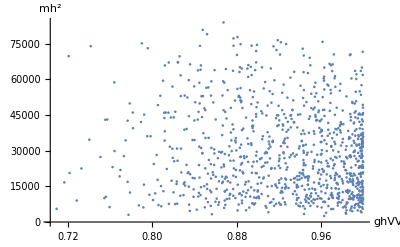

```mathematica
ListPlot[mass,AxesLabel->{ghVV,Indexed[m,h]^2}(*,PlotRange->{{0.99,1},{50,200}}*)]
```

## 4x4

```mathematica
Simplify[Solve[{D[V,v[1]]==0,D[V,v[2]]==0,D[V,v[3]]==0,D[V,v[4]]==0}, {μ[1,1],μ[2,2],μ[3,3],μ[4,4]} ]]//Simplify
```

{{μ[1,1]→1/v[1](v[1]^3 λ[1,1,1,1]+v[1] (v[2]^2 (λ[1,1,2,2]+λ[1,2,1,2]+λ[1,2,2,1])+v[3]^2 (λ[1,1,3,3]+λ[1,3,1,3]+λ[1,3,3,1])+v[4]^2 (λ[1,1,4,4]+λ[1,4,1,4]+λ[1,4,4,1]))-v[2] μ[1,2]-v[3] μ[1,3]-v[4] μ[1,4]),μ[2,2]→1/v[2](v[1]^2 v[2] (λ[1,1,2,2]+λ[1,2,1,2]+λ[1,2,2,1])+v[2]^3 λ[2,2,2,2]+v[2] (v[3]^2 (λ[2,2,3,3]+λ[2,3,2,3]+λ[2,3,3,2])+v[4]^2 (λ[2,2,4,4]+λ[2,4,2,4]+λ[2,4,4,2]))-v[1] μ[1,2]-v[3] μ[2,3]-v[4] μ[2,4]),μ[3,3]→v[1]^2 (λ[1,1,3,3]+λ[1,3,1,3]+λ[1,3,3,1])+v[2]^2 (λ[2,2,3,3]+λ[2,3,2,3]+λ[2,3,3,2])+v[3]^2 λ[3,3,3,3]+v[4]^2 λ[3,3,4,4]+v[4]^2 λ[3,4,3,4]+v[4]^2 λ[3,4,4,3]-(v[1] μ[1,3])/v[3]-(v[2] μ[2,3])/v[3]-(v[4] μ[3,4])/v[3],μ[4,4]→v[1]^2 (λ[1,1,4,4]+λ[1,4,1,4]+λ[1,4,4,1])+v[2]^2 (λ[2,2,4,4]+λ[2,4,2,4]+λ[2,4,4,2])+v[3]^2 λ[3,3,4,4]+v[3]^2 λ[3,4,3,4]+v[3]^2 λ[3,4,4,3]+v[4]^2 λ[4,4,4,4]-(v[1] μ[1,4])/v[4]-(v[2] μ[2,4])/v[4]-(v[3] μ[3,4])/v[4]}}

```mathematica
{μ[1,1],μ[2,2],μ[3,3],μ[4,4]}={1/v[1](v[1]^3 λ[1,1,1,1]+v[1] (v[2]^2 (λ[1,1,2,2]+λ[1,2,1,2]+λ[1,2,2,1])+v[3]^2 (λ[1,1,3,3]+λ[1,3,1,3]+λ[1,3,3,1])+v[4]^2 (λ[1,1,4,4]+λ[1,4,1,4]+λ[1,4,4,1]))-v[2] μ[1,2]-v[3] μ[1,3]-v[4] μ[1,4]),1/v[2](v[1]^2 v[2] (λ[1,1,2,2]+λ[1,2,1,2]+λ[1,2,2,1])+v[2]^3 λ[2,2,2,2]+v[2] (v[3]^2 (λ[2,2,3,3]+λ[2,3,2,3]+λ[2,3,3,2])+v[4]^2 (λ[2,2,4,4]+λ[2,4,2,4]+λ[2,4,4,2]))-v[1] μ[1,2]-v[3] μ[2,3]-v[4] μ[2,4]),v[1]^2 (λ[1,1,3,3]+λ[1,3,1,3]+λ[1,3,3,1])+v[2]^2 (λ[2,2,3,3]+λ[2,3,2,3]+λ[2,3,3,2])+v[3]^2 λ[3,3,3,3]+v[4]^2 λ[3,3,4,4]+v[4]^2 λ[3,4,3,4]+v[4]^2 λ[3,4,4,3]-(v[1] μ[1,3])/v[3]-(v[2] μ[2,3])/v[3]-(v[4] μ[3,4])/v[3],v[1]^2 (λ[1,1,4,4]+λ[1,4,1,4]+λ[1,4,4,1])+v[2]^2 (λ[2,2,4,4]+λ[2,4,2,4]+λ[2,4,4,2])+v[3]^2 λ[3,3,4,4]+v[3]^2 λ[3,4,3,4]+v[3]^2 λ[3,4,4,3]+v[4]^2 λ[4,4,4,4]-(v[1] μ[1,4])/v[4]-(v[2] μ[2,4])/v[4]-(v[3] μ[3,4])/v[4]};
```

```mathematica
MassMatrix4=Table[D[D[V,H[i]],H[j]],{i,n},{j,n}]/.H[i_]->0;
```

```mathematica
{{a,c1,c2,c3},{c1,b,0,0},{c2,0,c,0},{c3,0,0,d}}=MassMatrix4
```

Set::setraw: Cannot assign to raw object 0.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

```mathematica
mass={};
mu=500^2;
lambda=0.13;
count4=0;
countalign4=0;
For[i=1,i<=1000,i++,
(*Giving random values*)
For[a1=1,a1<=n,a1++,For[b1=1,b1<=n,b1++,μ[a1,b1]=RandomReal[{0.5, 1.5}]*mu ]];
For[a1=1,a1<=n,a1++,For[b1=1,b1<=n,b1++,For[cm=1,cm<=n,cm++,For[dm=1,dm<=n,dm++,λ[a1,b1,cm,dm]=RandomReal[{0.5, 1.5}]*lambda ]]]];
β[1]=RandomReal[{0, 1}];
β[2]=RandomReal[{0, 1}];
β[3]=RandomReal[{0, 1}];
v=RandomReal[{0.5, 1.5}]*246; 
(*Print[{a,b}];
Print[Cos[θ[1]]Cos[θ[2]]];*)
AppendTo[mass,{Cos[θ[1]]Cos[θ[2]]Cos[θ[3]],Eigenvalues[MassMatrix4][[4]]}];
If[Cos[θ[1]]Cos[θ[2]]Cos[θ[3]]>=0.96 && Eigenvalues[MassMatrix4][[4]]<15000,countalign4++];
If[Eigenvalues[MassMatrix4][[4]]<15000,count4++]]
```

```mathematica
count4
countalign4
```

281

81

```mathematica
MinMax[mass[[All,2]]]
```

{2431.91,91892.6}

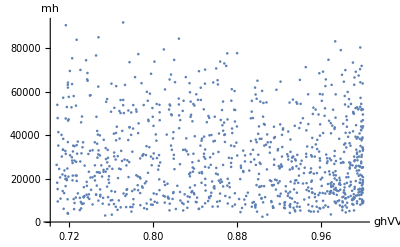

```mathematica
ListPlot[mass,AxesLabel->{ghVV,Indexed[m,h]}(*,PlotRange->{{0.99,1},{50,200}}*)]
```